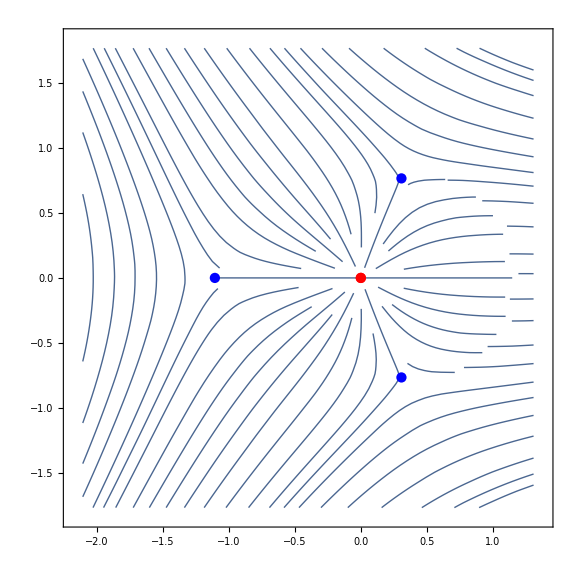
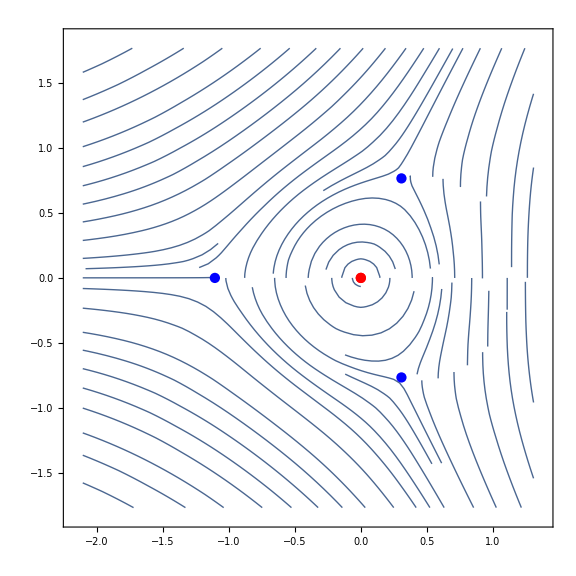

```mathematica
δ=0.7;
potential=Function[x,-(δ^2+x+3/(4 x^2))];
StokesGraph[potential,1]
Clear[δ,potential];
```

{-1.38883,0.194416+0.708678 ⅈ,0.194416-0.708678 ⅈ}

0.804431-1.55939 ⅈ

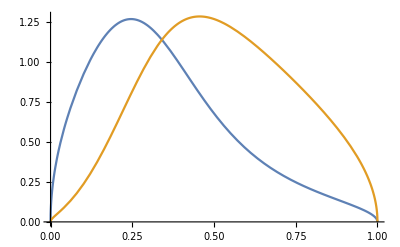
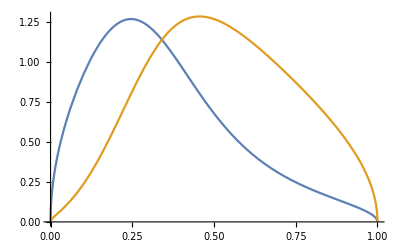

```mathematica
δ=1;
potential=Function[x,-(δ^2+x+3/(4 x^2))];
zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
b=zeros⟦1⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,b,f,zeros,chunks,sqrtf,potential];
```

```mathematica
(*Constructing ab function for β==0*)
δbegining=-2;δend=2;δnstep=300;IabList={};
potential=Function[{x,δ},-3/(4 x^2)-x-δ^2];
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,

zeros=NSolve[potential[z,δ]==0,z]//Quiet;

a=z/.zeros⟦3⟧;
b=z/.zeros⟦1⟧;

f=Function[t,potential[line[a,b][t],δ]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ab=NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}];
AppendTo[IabList,{δ,ab}];

];

IabFunc=Interpolation[IabList];
Clear[δ,a,b,ab,f,chunks,sqrtf,potential,zeros];
```

```mathematica
(*Constructing ac function for β==0*)
δbegining=-2;δend=2;δnstep=300;IacList={};
potential=Function[{x,δ},-3/(4 x^2)-x-δ^2];
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,

zeros=NSolve[potential[z,δ]==0,z]//Quiet;

a=z/.zeros⟦3⟧;
c=z/.zeros⟦2⟧;

f=Function[t,potential[line[a,c][t],δ]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ac=NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}];
AppendTo[IacList,{δ,ac}];

];

IacFunc=Interpolation[IacList];
Clear[δ,a,c,ac,f,chunks,sqrtf,potential,zeros];
```

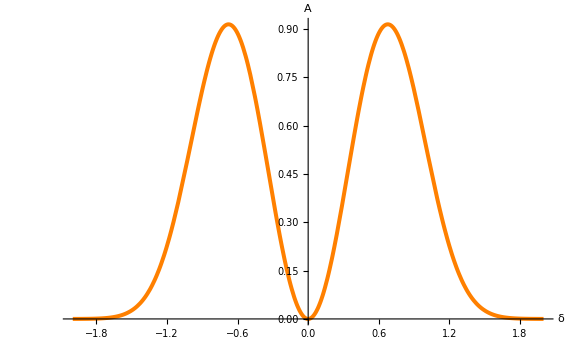

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,

R=ⅇ^(-2 IabFunc[δ]) Subscript[s, 1]+Subscript[s, 2]/.{Subscript[s, 1]->2ⅈ ⅇ^(2IabFunc[0]),Subscript[s, 2]->-ⅈ}//Quiet;
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ(*,a,b,ab,ab0,f,chunks,sqrtf,potential,zeros*)];
(*ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Large]*)
Plot[Interpolation[Dissipation][x],{x,-2,2},
PlotRange->Full,
AxesLabel->{Style["δ",FontSize->40,Black],Style["A",FontSize->40,Black]},
ImageSize->Large,
LabelStyle->{FontSize->20},
PlotStyle->{Orange,Thickness[0.005]}]
```

```mathematica
F=({{ⅇ^-i, ⅇ^i/r}, {0, ⅇ^i}});(*r->1/(b+aⅇ^(-2i)),F=S[b]ᵀ.W[-i].S[a]ᵀ*)
P=({{ⅇ^up, u ⅇ^-up}, {0, ⅇ^-up}});
F.Inverse[A].{1,0};
%⟦2⟧/%⟦1⟧//Simplify
A.F*.A.P.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
```

r

1/Conjugate[r]

```mathematica
A.Inverse[F].A.F*.A.P.{1,0};
Inverse[P].Inverse[A].Inverse[F*].Inverse[A].F.Inverse[A].{1,0};
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦2⟧+%%⟦1⟧ⅇ^(4/3 ρ^(3/2))), -1, -(Log[ρ]+2π ⅈ)}, {ⅈ(%⟦2⟧+%⟦1⟧ⅇ^(4/3 ρ^(3/2))), -1, -(Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
D[%,ρ]/(2 √ρ)ⅇ^(-4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(4/3 ρ^(3/2))//Simplify

A.Inverse[F].A.F*.A.P.{0,1};
Inverse[P].Inverse[A].Inverse[F*].Inverse[A].F.Inverse[A].{0,1};
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦2⟧ⅇ^(-4/3 ρ^(3/2))+%%⟦1⟧), -1, -(Log[ρ]+2π ⅈ)}, {ⅈ(%⟦2⟧ⅇ^(-4/3 ρ^(3/2))+%⟦1⟧), -1, -(Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
-D[%,ρ]/(2 √ρ)ⅇ^(4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(-4/3 ρ^(3/2))//Simplify
```

-(2 ⅈ ⅇ^(-i-up-Conjugate[i]) π (ⅇ^(2 (up+Conjugate[i])) r+ⅇ^(2 (i+Conjugate[i])) u+ⅇ^(2 i) Conjugate[r]-ⅇ^(2 (i+Conjugate[i])) r u Conjugate[r]))/(r Conjugate[r])

-(4 ⅈ π (-ⅇ^(i+up+Conjugate[i])+(1+ⅇ^(i+up+Conjugate[i])) r Conjugate[r]))/(r Conjugate[r])

(2 ⅈ ⅇ^(-i-up-Conjugate[i]) π (ⅇ^(2 (up+Conjugate[i])) r+ⅇ^(2 (i+Conjugate[i])) u+ⅇ^(2 i) Conjugate[r]-ⅇ^(2 (i+Conjugate[i])) r u Conjugate[r]))/(r Conjugate[r])

-(4 ⅈ ⅇ^(-i-up-Conjugate[i]) π (ⅇ^(2 Conjugate[i]) u+(1+ⅇ^(i+up+Conjugate[i])) Conjugate[r]))/Conjugate[r]

```mathematica
F=({{ⅇ^i, 0}, {r ⅇ^i, ⅇ^-i}});(*r->b+aⅇ^(-2i),F=S[b].W[i].S[a]*)
P=({{ⅇ^up, u ⅇ^-up}, {0, ⅇ^-up}});
F.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
F*.P.{1,0};
%⟦1⟧/%⟦2⟧//Simplify
```

r

1/Conjugate[r]

```mathematica
Inverse[J.F*.J]*.F*.P.{1,0};
J.P*.J.Inverse[J.F*.J].F.{1,0};
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦2⟧+%%⟦1⟧ⅇ^(4/3 ρ^(3/2))), -1, -(Log[ρ]+2π ⅈ)}, {ⅈ(%⟦2⟧+%⟦1⟧ⅇ^(4/3 ρ^(3/2))), -1, -(Log[ρ]-2π ⅈ)}})/.up*->-up/.u*->-u ⅇ^(-2up)/.u->ⅈ υ ⅇ^up//Det//Simplify//Apart;
D[%,ρ]/(2 √ρ)ⅇ^(-4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(4/3 ρ^(3/2))//Simplify

Inverse[J.F*.J]*.F*.P.{0,1};
J.P*.J.Inverse[J.F*.J].F.{0,1};
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦2⟧ⅇ^(-4/3 ρ^(3/2))+%%⟦1⟧), -1, -(Log[ρ]+2π ⅈ)}, {ⅈ(%⟦2⟧ⅇ^(-4/3 ρ^(3/2))+%⟦1⟧), -1, -(Log[ρ]-2π ⅈ)}})/.up*->-up/.u*->-u ⅇ^(-2up)/.u->ⅈ υ ⅇ^up//Det//Simplify//Apart;
-D[%,ρ]/(2 √ρ)ⅇ^(4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(-4/3 ρ^(3/2))//Simplify
```

0

2 π (-2 ⅈ+ⅇ^(i-up-Conjugate[i]) r-ⅈ ⅇ^(i+Conjugate[i]) υ+(-ⅇ^(-i+up+Conjugate[i])+ⅈ ⅇ^(i+Conjugate[i]) r υ) Conjugate[r])

0

2 π (-2 ⅈ+ⅇ^(i-up-Conjugate[i]) r-ⅈ ⅇ^(i+Conjugate[i]) υ+(-ⅇ^(-i+up+Conjugate[i])+ⅈ ⅇ^(i+Conjugate[i]) r υ) Conjugate[r])

```mathematica
u->ⅈ υ ⅇ^up
```

```mathematica
-2 ⅈ+ⅇ^(2Im[i]-up) r-ⅈ ⅇ^(2Re[i]) υ+(-ⅇ^(-2Im[i]+up)+ⅈ ⅇ^(2Re[i]) r υ) Conjugate[r]==0
```

```mathematica
ⅈ(υ (Abs[r]^2-1)ⅇ^(2Re[i])-2)+r ⅇ^(2Im[i]-up) -r ⅇ^(-2Im[i]+up)==0
```

```mathematica
r ⅇ^-up+r* ⅇ^up==0
```

```mathematica
Solve[ρ^2 υ ⅇ^(2Re[i])+ρ(ⅇ^(2Im[i])- ⅇ^(-2Im[i]))-(2+υ ⅇ^(2Re[i]))==0,ρ]//Simplify
```

{{ρ→(ⅇ^(-2 Re[i]) (ⅇ^(-2 Im[i])-ⅇ^(2 Im[i])-√(-2+ⅇ^(-4 Im[i])+ⅇ^(4 Im[i])+8 ⅇ^(2 Re[i]) υ+4 ⅇ^(4 Re[i]) υ^2)))/(2 υ)},{ρ→(ⅇ^(-2 Re[i]) (ⅇ^(-2 Im[i])-ⅇ^(2 Im[i])+√(-2+ⅇ^(-4 Im[i])+ⅇ^(4 Im[i])+8 ⅇ^(2 Re[i]) υ+4 ⅇ^(4 Re[i]) υ^2)))/(2 υ)}}

```mathematica
{{ρ->(ⅇ^(-2 Re[i]) (ⅇ^(-2 Im[i])-ⅇ^(2 Im[i])-√(4(ⅇ^(2 Re[i]) υ+1)^2+ⅇ^(-4 Im[i])+ⅇ^(4 Im[i])-6)))/(2 υ)},{ρ->(ⅇ^(-2 Re[i]) (ⅇ^(-2 Im[i])-ⅇ^(2 Im[i])+√(4(ⅇ^(2 Re[i]) υ+1)^2+ⅇ^(-4 Im[i])+ⅇ^(4 Im[i])-6)))/(2 υ)}}
```

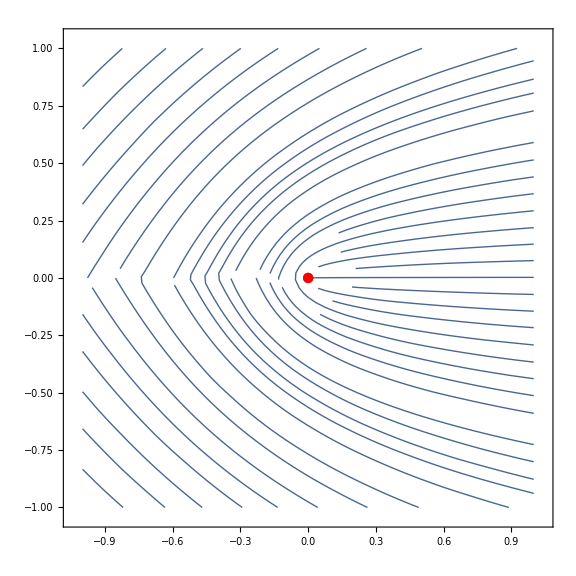
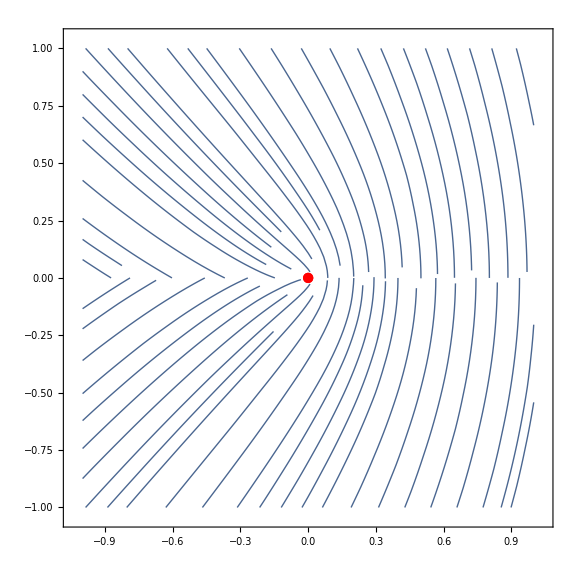

```mathematica
δ=0.7;
potential=Function[x,-(√x+δ^2)/x];
StokesGraph[potential,1]
Clear[δ,potential];
```

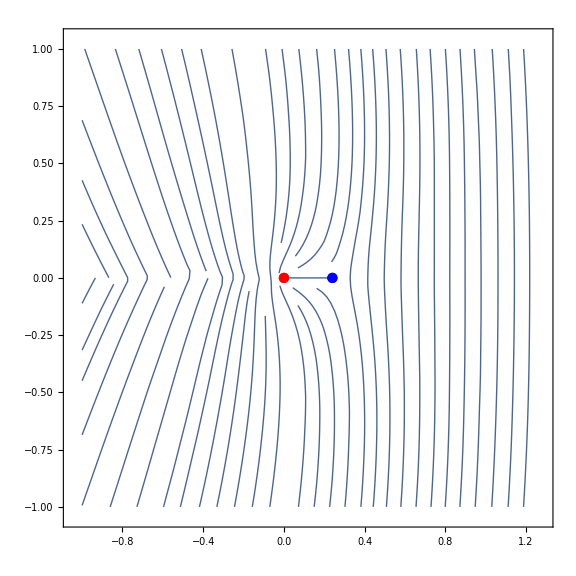
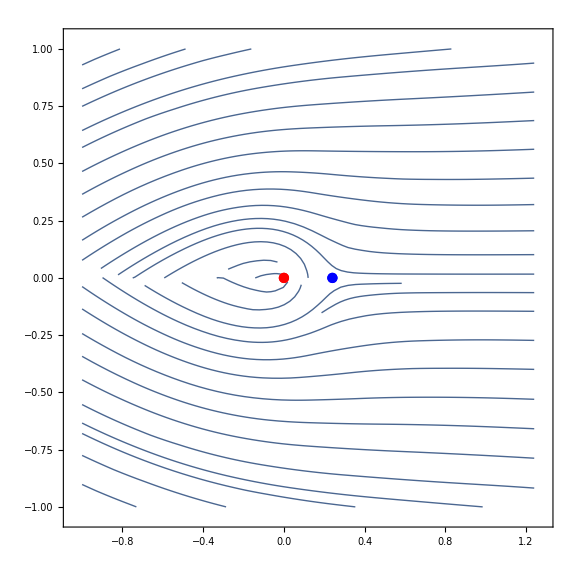

```mathematica
δ=0.7;
potential=Function[x,-(-√x+δ^2)/x];
StokesGraph[potential,1]
Clear[δ,potential];
```

```mathematica
F=S[r].W[4/3 δ^3];
P=S[ⅈ p]ᵀ;
F.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
F*.P.{1,0};
%⟦1⟧/%⟦2⟧//Simplify
```

r

1/Conjugate[r]

```mathematica
Inverse[J.F*.J]*.F*.P.{1,0};
(J.P*.J).Inverse[J.F*.J].F.{1,0};
({{1, 1, Log[ρ]}, {ⅈ(%%⟦1⟧ⅇ^(-8/3 ρ^(3/4))+%%⟦2⟧), 1, (Log[ρ]+4π ⅈ)}, {-ⅈ(%⟦1⟧ⅇ^(-8/3 ρ^(3/4))+%⟦2⟧), 1, (Log[ρ]-4π ⅈ)}})/.δ*->δ/.p*->p//Det//Simplify//Apart;
-D[%,ρ]/2 ρ^(1/4)ⅇ^(8/3 ρ^(3/4))//Simplify
%%-%ⅇ^(-8/3 ρ^(3/4))//Simplify

Inverse[J.F*.J]*.F*.P.{0,1};
(J.P*.J).Inverse[J.F*.J].F.{0,1};
({{1, 1, Log[ρ]}, {ⅈ(%%⟦1⟧+%%⟦2⟧ⅇ^(8/3 ρ^(3/4))), 1, (Log[ρ]+4π ⅈ)}, {-ⅈ(%⟦1⟧+%⟦2⟧ⅇ^(8/3 ρ^(3/4))), 1, (Log[ρ]-4π ⅈ)}})/.δ*->δ/.p*->p//Det//Simplify//Apart;
D[%,ρ]/2 ρ^(1/4) ⅇ^(-8/3 ρ^(3/4))//Simplify
%%-%ⅇ^(8/3 ρ^(3/4))//Simplify
```

0

4 π (-2 ⅈ+r-Conjugate[r]+ⅈ ⅇ^((8 δ^3)/3) p (-1+r Conjugate[r]))

0

4 π (-2 ⅈ+r-Conjugate[r]+ⅈ ⅇ^((8 δ^3)/3) p (-1+r Conjugate[r]))

```mathematica
-2 ⅈ+2Im[r]+ⅈ ⅇ^((8 δ^3)/3) p (-1+r Conjugate[r])==0;
ⅇ^((8 δ^3)/3) p a+2==0;
a->-2/p ⅇ^(-8/3 δ^3)
```

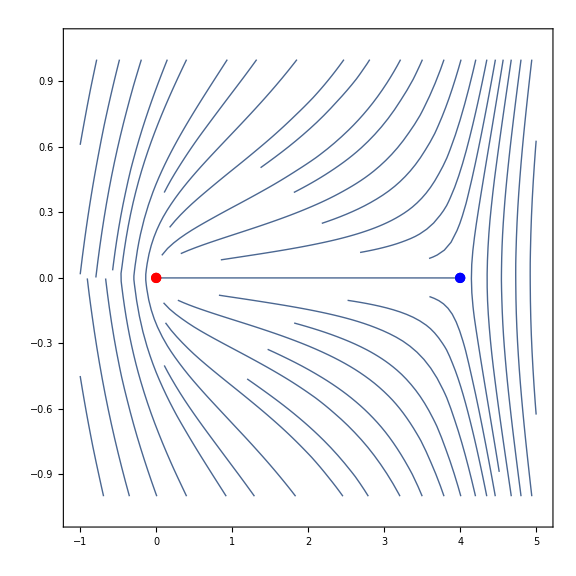
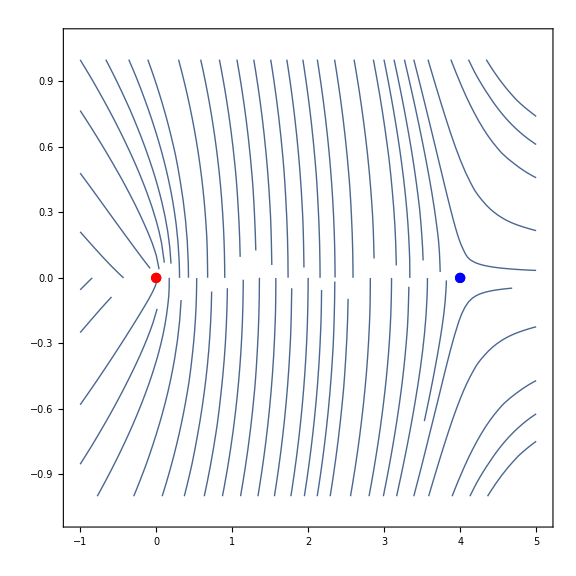

```mathematica
δ=0.7;l=2;
potential=Function[x,-(√x+δ^2)/x(1-(√x)/l)];
StokesGraph[potential,1]
Clear[δ,l,potential];
```

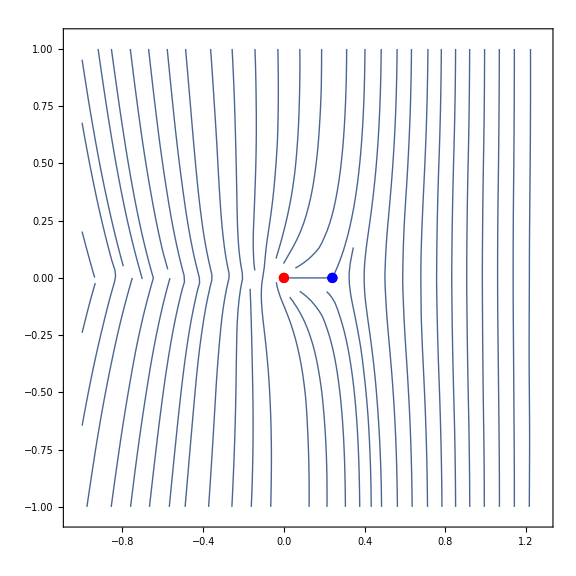
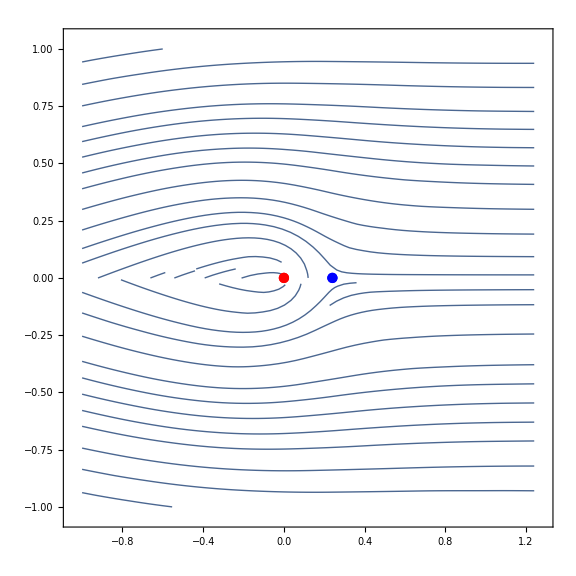

```mathematica
δ=0.7;l=2;
potential=Function[x,-(-√x+δ^2)/x(1+(√x)/l)];
StokesGraph[potential,1]
Clear[δ,l,potential];
```

```mathematica
F=({{ⅇ^(L+(4 δ^3)/3), 0}, {(ⅇ^(L+(4 δ^3)/3))/r, ⅇ^(-L-(4 δ^3)/3)}});(*S[b].W[4/3 δ^3].W[-L].S[a]*)
F.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2
```

1-Abs[r]^2-ⅇ^(2 Re[-L-(4 δ^3)/3]) Abs[r]^2

```mathematica
Inverse[F].J.F*.J.{1,0};
Inverse[J.F*.J].F.{1,0};
({{1, 1, Log[ρ]}, {(%%⟦1⟧+%%⟦2⟧ⅇ^(-2ⅈ ρ)), 1, (Log[ρ]+4π ⅈ)}, {(%⟦1⟧+%⟦2⟧ⅇ^(-2ⅈ ρ)), 1, (Log[ρ]-4π ⅈ)}})/.δ*->δ/.L*->L//Det//Simplify//Apart;
D[%,ρ]/(-2ⅈ)ⅇ^(2ⅈ ρ)//Simplify
%%-%ⅇ^(-2ⅈ ρ)//Simplify

Inverse[F].J.F*.J.{0,1};
Inverse[J.F*.J].F.{0,1};
({{1, 1, Log[ρ]}, {(%%⟦1⟧ⅇ^(2ⅈ ρ)+%%⟦2⟧), 1, (Log[ρ]+4π ⅈ)}, {(%⟦1⟧ⅇ^(2ⅈ ρ)+%⟦2⟧), 1, (Log[ρ]-4π ⅈ)}})/.δ*->δ/.L*->L//Det//Simplify//Apart;
D[%,ρ]/(2ⅈ)ⅇ^(-2ⅈ ρ)//Simplify
%%-%ⅇ^(2ⅈ ρ)//Simplify
```

0

-4 ⅈ π (2-ⅇ^(-2 L-(8 δ^3)/3)+(ⅇ^(2 L+(8 δ^3)/3) (1-r Conjugate[r]))/(r Conjugate[r]))

0

-4 ⅈ π (2-ⅇ^(-2 L-(8 δ^3)/3)+(ⅇ^(2 L+(8 δ^3)/3) (1-r Conjugate[r]))/(r Conjugate[r]))

```mathematica
Solve[2-ⅇ^(-2 L-(8 δ^3)/3)+(ⅇ^(2 L+(8 δ^3)/3) (1-(1-a)/(1+ⅇ^(-2 (L+(4 δ^3)/3)))))/((1-a)/(1+ⅇ^(-2 (L+(4 δ^3)/3))))==0,a]
```

{{a→-(-1+3 ⅇ^(2 L+(8 δ^3)/3))/((-1+ⅇ^(2 L+(8 δ^3)/3))^2)}}

```mathematica
U[Function[x,-(x+δ^2+3/(4 x^2))(1-x/l)],√x,x][z]//FullSimplify
```

(3+4 z (√z+δ^2)-4 l (z+√z δ^2))/(16 l z^(3/2))

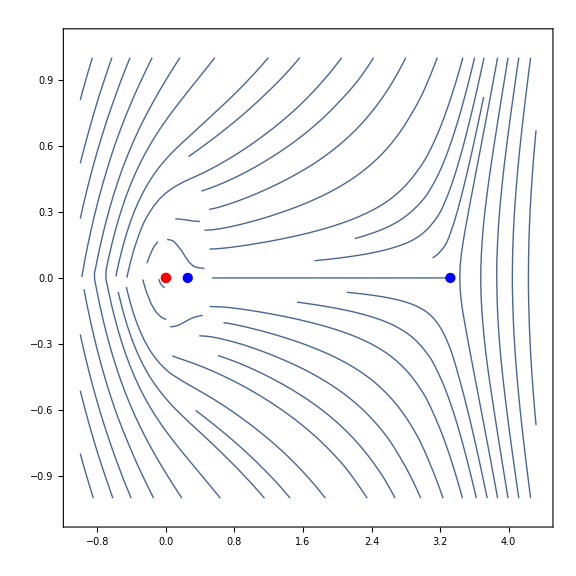
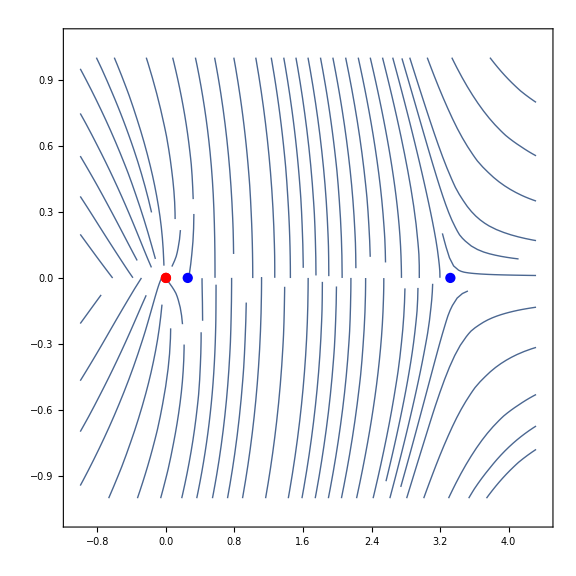

```mathematica
δ=0.7;l=2;
potential=Function[z,(3+4 √z(√z -l)(√z+ δ^2))/(16 l z^(3/2))];
StokesGraph[potential,1]
Clear[δ,l,potential];
```

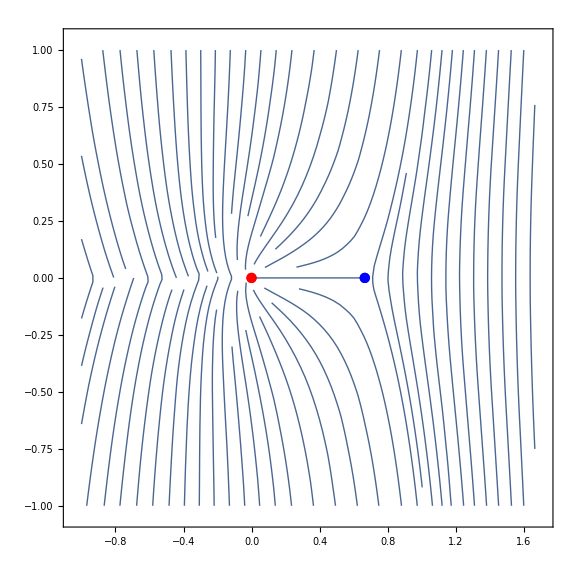
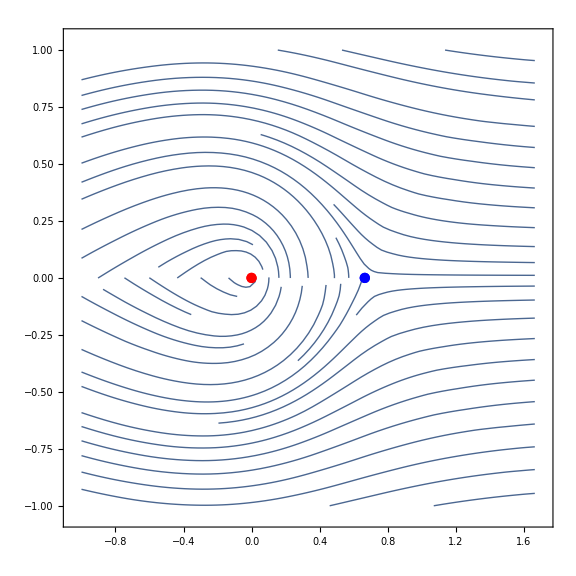

```mathematica
δ=0.7;l=2;
potential=Function[z,-(3+4 √z(√z +l)(-√z+ δ^2))/(16 l z^(3/2))];
StokesGraph[potential,1]
Clear[δ,l,potential];
```